## Question 1

### Part A

```mathematica
P := ({{0.45, 0.35, 0.20}, {0.36, 0.34, 0.30}, {0.25, 0.65, 0.1}})
```

### Part B

```mathematica
outcomes := {{"Day", "Sunny", "Rainy", "Overcast"}}
For[day= 0, day<=5, day++,
AppendTo[
outcomes,
{
day,
({{1, 0, 0}}).MatrixPower[P,day]//MatrixForm//TraditionalForm,
({{0, 1, 0}}).MatrixPower[P,day]//MatrixForm//TraditionalForm,
({{0, 0, 1}}).MatrixPower[P,day]//MatrixForm//TraditionalForm
}]
]
Grid[outcomes,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Day | Sunny | Rainy | Overcast
0 | (1. | 0. | 0.) | (0. | 1. | 0.) | (0. | 0. | 1.)
1 | (0.45 | 0.35 | 0.2) | (0.36 | 0.34 | 0.3) | (0.25 | 0.65 | 0.1)
2 | (0.3785 | 0.4065 | 0.215) | (0.3594 | 0.4366 | 0.204) | (0.3715 | 0.3735 | 0.255)
3 | (0.370415 | 0.410435 | 0.21915) | (0.369906 | 0.406834 | 0.22326) | (0.365385 | 0.422765 | 0.21185)
4 | (0.369231 | 0.411641 | 0.219129) | (0.368733 | 0.41291 | 0.218357) | (0.369581 | 0.409327 | 0.221092)
5 | (0.369127 | 0.411622 | 0.219251) | (0.369167 | 0.411378 | 0.219455) | (0.368942 | 0.412234 | 0.218824)

```mathematica
verdict :={
{"Day", "Sunny", "Rainy", "Overcast"},
{"0", "Sunny", "Rainy", "Rainy"},
{"1","Sunny","Sunny","Rainy"},
{"2","Rainy","Rainy","Rainy"},
{"3","Rainy","Rainy","Rainy"},
{"4","Rainy","Rainy","Rainy"},
{"5","Rainy","Rainy","Rainy"}
}
Grid[verdict,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Day | Sunny | Rainy | Overcast
0 | Sunny | Rainy | Rainy
1 | Sunny | Sunny | Rainy
2 | Rainy | Rainy | Rainy
3 | Rainy | Rainy | Rainy
4 | Rainy | Rainy | Rainy
5 | Rainy | Rainy | Rainy

### Part C

```mathematica
(({{0, 1, 0}}).P)^5//MatrixForm//TraditionalForm
```

(0.03125 | 0.000976563 | 0.000976563)

```mathematica
(({{0, 0, 1}}).P)^5//MatrixForm//TraditionalForm
```

(0.0503284 | 0.00525219 | 0.00001)

```mathematica
({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})^5//MatrixForm
```

(1 | 32 | 243
1024 | 3125 | 7776
16807 | 32768 | 59049)

```mathematica
MatrixPower[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}),5]//MatrixForm
```

(121824 | 149688 | 177552
275886 | 338985 | 402084
429948 | 528282 | 626616)

```mathematica
testlist := {{"a"}, {"b"}, {"c"}}
```

```mathematica
AppendTo[testlist[],{1, 2, 3}]
```

Set::noval: Symbol testlist in part assignment does not have an immediate value.

{a,{1,2,3}}

```mathematica
AppendTo[testlist,{1, 2, 3}]
```

{{1,2,3},{1,2,3}}

## Question 2

```mathematica
X:=DiscreteMarkovProcess[{1, 0, 0},{{0.45,0.35,0.2},{0.5,0.25,0.25},{0.55,0.35,0.1}}]
```

```mathematica
PDF[StationaryDistribution[X],1]
```

0.485537

```mathematica
X[2]
```

DataDistribution[…]

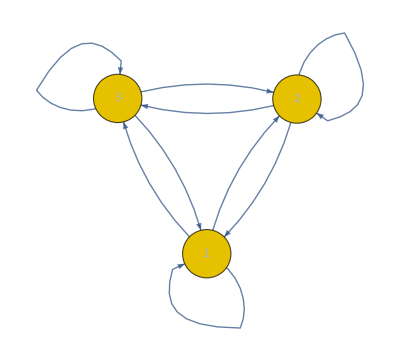

```mathematica
Graph[X]
```

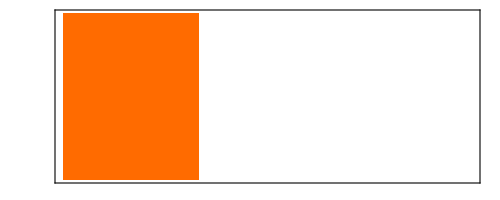
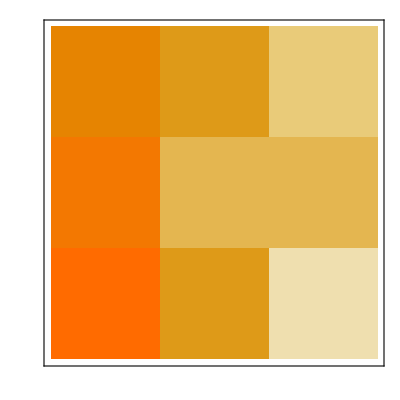
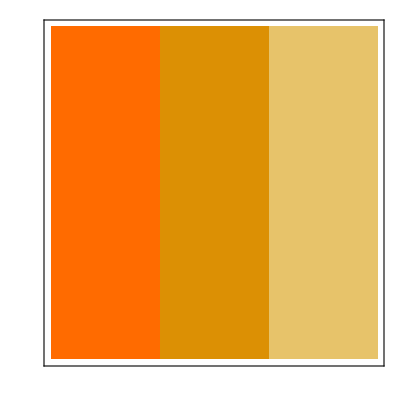
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0.818182,0.333333,0.111111}
HoldingTimeVariance | {1.4876,0.444444,0.123457}
Structural Properties | 
CommunicatingClasses | {1,2,3}
RecurrentClasses | {1,2,3}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Primitive | True
Aperiodic | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[X]
```